```mathematica
n=Log[alpha(1-beta)/k/beta +1]/Log[1+alpha]
```

Log[1+(alpha (1-beta))/(beta k)]/Log[1+alpha]

```mathematica
Simplify[D[n,beta]]
```

alpha/(beta (alpha (-1+beta)-beta k) Log[1+alpha])

```mathematica
alpha/(beta (alpha (-1+beta)-beta k) Log[1+alpha])
```

alpha/(beta (alpha (-1+beta)-beta k) Log[1+alpha])

```mathematica
Simplify[D[D[n,beta],beta]]
```

(alpha (alpha-2 alpha beta+2 beta k))/(beta^2 (alpha (-1+beta)-beta k)^2 Log[1+alpha])

0.06

0.035

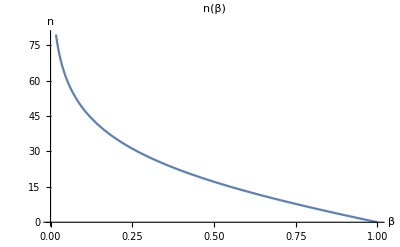

```mathematica
alpha=0.06
k=0.035
Plot[n,{beta,0,1},AxesLabel->{β, "n"},PlotLabel->"n(β)"]
```

-41.1883/(2.4 beta-1. beta^2)

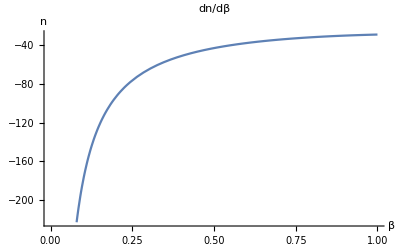

```mathematica
dnb = Simplify[D[n,beta]]
Plot[dnb,{beta,0,1},AxesLabel->{β, "n"},PlotLabel->"dn/dβ"]
```

(98.852-82.3767 beta)/((2.4-1. beta)^2 beta^2)

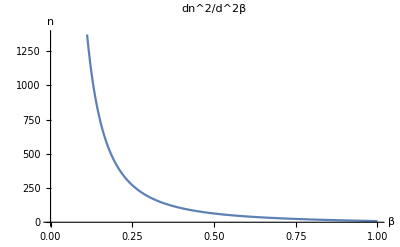

```mathematica
ddnb = Simplify[D[dnb,beta]]
Plot[ddnb,{beta,0,1},AxesLabel->{β, "n"},PlotLabel->"dn^2/d^2β"]
```